```mathematica
Clear[cIFull,cI,dirProd,cartProd,strProd,rootProd]

dirProd[G_Graph,H_Graph]:=AdjacencyGraph[KroneckerProduct[AdjacencyMatrix[G],AdjacencyMatrix[H]],VertexLabels->"Index"]
cartProd[G_Graph,H_Graph]:=Module[{n,m},n=VertexCount[G];m=VertexCount[H];
AdjacencyGraph[KroneckerProduct[AdjacencyMatrix[G],IdentityMatrix[m]]+KroneckerProduct[IdentityMatrix[n],AdjacencyMatrix[H]],VertexLabels->"Index"]]
strProd[G_Graph,H_Graph]:=Module[{n,m,Ad},n=VertexCount[G];m=VertexCount[H];
Ad=KroneckerProduct[AdjacencyMatrix[G]+IdentityMatrix[n],AdjacencyMatrix[H]+IdentityMatrix[m]]-IdentityMatrix[n*m];
AdjacencyGraph[Ad,VertexLabels->"Index"]]
rootProd[G_Graph,H_Graph,rt_: 1]:=Module[{n,m,rtAd,Ad},n=VertexCount[G];m=VertexCount[H];
rtAd=ConstantArray[0,{m,m}];
rtAd[[rt,rt]]=1;
Ad=KroneckerProduct[IdentityMatrix[n],AdjacencyMatrix[H]]+KroneckerProduct[AdjacencyMatrix[G],rtAd];
AdjacencyGraph[Ad,VertexLabels->"Index"]]

cIFull[G_Graph]:=CIMult@@PauliActionCC[G,VertexCount[G]-1,0.19,False]
cI[G_Graph]:=CIMult@@PauliActionCC[G,VertexCount[G]-1,0.19,True]
```

```mathematica
H=StarGraph[2];
K=CompleteGraph[3];
```

```mathematica
cI[dirProd[K,H]]
cIFull[dirProd[K,H]]
```

Nested symmetry group detected. Compiling for nauty's canonical image provider.

setting up parallel build directory: /store/DAMTP/jkrb2/programming/CoffeeCode/build/release-21724745353915055424.0/

-0.00323692

-0.00323692

```mathematica
cI[strProd[K,H]]
cIFull[strProd[K,H]]
```

Product symmetry group with single hairs detected. Compiling for trivial canonical image provider.

0.000155469

0.000155469

```mathematica
cI[cartProd[K,H]]
cIFull[cartProd[K,H]]
```

Nested symmetry group detected. Compiling for nauty's canonical image provider.

-0.00128705

-0.00128705

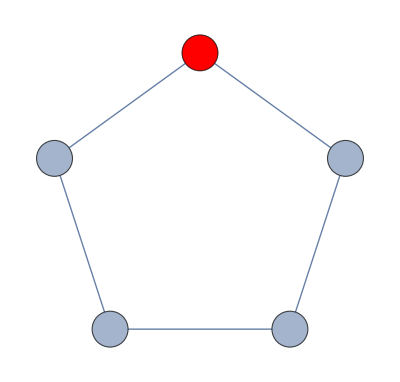
```mathematica
cI[-Graphics-]
```

Nested symmetry group detected. Compiling for nauty's canonical image provider.

-0.00529781

```mathematica
cIFull[-Graphics-]
```

-0.00529781

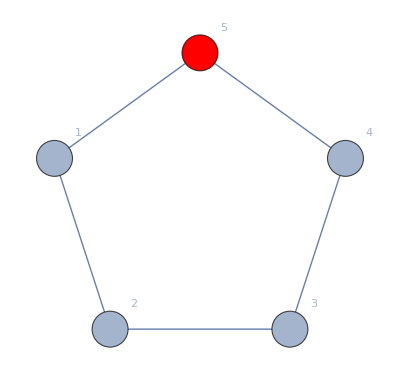

PermutationGroup[{Cycles[{{1,4},{2,3}}]}]

```mathematica
EnvironmentPlot[Graph[{1,2,3,4,5},{1<->2,2<->3,3<->4,4<->5,5<->1}],4,"Index"]
GroupForGraph[%,4]
```

```mathematica
GraphStateApplyChannel[-Graphics-,4]["λ"]//EchoAssoc[5]
```

PermutationGroup[{Cycles[{{1,4},{2,3}}]}]

00000 | 1+2 q1 q2^2+q1^2 q2^2+2 q1 q3^2+q1^2 q3^2+q2^2 q3^2
00001 | 2 q1 q3+2 q1^2 q3+2 q2^2 q3+2 q1 q2^2 q3
01000 | q1^2 q2+q1 q2^3+q3+q1 q3+q1^2 q3+q1 q2^2 q3+q2 q3^2+q1 q2 q3^2
01001 | q1+q2^2+2 q1 q2 q3+q1^2 q2 q3+q2^3 q3+q1 q3^2+q1^2 q3^2
01100 | q1^2+q2^4+2 q2 q3+2 q1^2 q2 q3+q3^2+q1^2 q3^2
01101 | 2 q1 q2+2 q1 q3+2 q1 q2^2 q3+2 q1 q2 q3^2
10000 | q1^2 q2+q1^3 q2+q2^3+q3+q1 q3+q2^2 q3+q1 q2 q3^2+q1 q3^3
10001 | q1^2+q1 q2^2+q2 q3+2 q1 q2 q3+q1^2 q2 q3+q1 q3^2+q2^2 q3^2
10010 | q1^4+q2^2+2 q1 q2^2+q3^2+2 q1 q3^2+q2^2 q3^2
10011 | 2 q1 q2+2 q1^2 q2+2 q2 q3^2+2 q1 q2 q3^2
10100 | q1+q1 q2^2+q1^2 q2^2+2 q1 q2 q3+q1^2 q2 q3+q3^2+q2 q3^3
10101 | q1 q2+q2^3+q1 q3+q1^2 q3+q1^3 q3+q2^2 q3+q2 q3^2+q1 q2 q3^2
11000 | q1^3+q1^2 q2^2+q2 q3+2 q1 q2 q3+q2^3 q3+q3^2+q1 q3^2
11001 | q2+q1 q2+q1^2 q2+q1^2 q3+q2^2 q3+q1 q2^2 q3+q1 q2 q3^2+q1 q3^3
11010 | q1 q2+q1^2 q2+q1^3 q2+q1 q3+q2^2 q3+q1 q2^2 q3+q2 q3^2+q3^3
11011 | q1^3+q2^2+q1 q2^2+q2 q3+2 q1 q2 q3+q1^2 q3^2+q2 q3^3
11100 | q2+q1 q2+q1 q2^3+q1^2 q3+q1^3 q3+q1 q2^2 q3+q2 q3^2+q3^3
11101 | q1^2+q1 q2^2+q2 q3+2 q1 q2 q3+q1^2 q2 q3+q1 q3^2+q2^2 q3^2
11110 | q1^2+q2^2+q1^2 q2^2+2 q2 q3+2 q1^2 q2 q3+q3^4
11111 | 2 q1^2 q2+2 q1^2 q3+2 q2^2 q3+2 q2 q3^2

```mathematica
CIMult@@PauliAction[-Graphics-,4,0.19]
```

-0.00529781

```mathematica
TuplesForGraph[2,-Graphics-,4,4]
%⟦"tuples"⟧//Length
```

PermutationGroup[{Cycles[{{1,4},{2,3}}]}]

<|tuples→{{1,1,1,1},{2,1,1,1},{2,2,1,1},{2,2,2,1},{2,2,2,2},{2,2,1,2},{2,1,2,1},{2,1,1,2},{1,2,1,1},{1,2,2,1}},multiplicities→{1,2,2,2,1,2,2,1,2,1}|>

10

```mathematica
With[{
group=PermutationGroup[{Cycles[{{1,4},{2,3}}]}]
},

Tuples[{1,2},4]//DeleteDuplicatesBy[Sort@GroupOrbits[group,{#},Permute]&]
]
%//Length
```

{{1,1,1,1},{1,1,1,2},{1,1,2,1},{1,1,2,2},{1,2,1,2},{1,2,2,1},{1,2,2,2},{2,1,1,2},{2,1,2,2},{2,2,2,2}}

10

```mathematica
group=PermutationGroup[{Cycles[{{1,4},{2,3}}]}]
CanonicalOrderQ[group]/@{{1,1,1,1},{2,1,1,1},{2,2,1,1},{2,2,2,1},{2,2,2,2},{2,2,1,2},{2,1,2,1},{2,1,2,2},{2,1,1,2},{1,2,1,1},{1,2,2,1},{1,1,2,1}}

Tuples[{1,2},4]//Select@CanonicalOrderQ[group]
```

PermutationGroup[{Cycles[{{1,4},{2,3}}]}]

{True,True,True,True,True,True,True,False,True,True,True,False}

{{1,1,1,1},{1,2,1,1},{1,2,2,1},{2,1,1,1},{2,1,1,2},{2,1,2,1},{2,2,1,1},{2,2,1,2},{2,2,2,1},{2,2,2,2}}

```mathematica
SGSTransversal@group
```

{{1}→PermutationGroup[{Cycles[{{1,4},{2,3}}]}],{4}→PermutationGroup[{}]}

```mathematica
stabchain=GroupStabilizerChain@group

strongGS=GroupGenerators[stabchain[[1,-1]]]
```

{{}→PermutationGroup[{Cycles[{{1,4},{2,3}}]}],{1}→PermutationGroup[{}]}

{Cycles[{{1,4},{2,3}}]}

```mathematica
CanonicalOrderQ[group][{1,1,2,1}]
```

SGS {1}→PermutationGroup[{Cycles[{{1,4},{2,3}}]}]

v_i {1}

children {{1,1,2,1},{1,2,1,1}}

cv_i {1}

cv_i {1}

SGS {4}→PermutationGroup[{}]

v_i {1,1,2,1}

children {{1,1,2,1}}

cv_i {1,1,2,1}

children {{1,2,1,1}}

cv_i {1,2,1,1}

False